Introduction to Mathematica - Examples

This will clear all definitions:

```mathematica
ClearAll["Global`*"]
```

Calculations

```mathematica
6/5.0
```

1.2

```mathematica
5^2
```

25

```mathematica
N[√5]
```

2.23607

```mathematica
(1+2-9)/7.0
```

-0.857143

```mathematica
(6.67*^-11*5.972*^24*70)/((6.371*^6)^2)
```

6.67×10^-11

```mathematica
π*2.
```

6.28319

```mathematica
6.67*10^-11
```

6.67×10^-11

Variables

```mathematica
ω
```

8

```mathematica
m=70;
REarth = 6.371*^6;
mEarth = 5.972*^24;
GravConstant = 6.67*^-11;
```

```mathematica
(GravConstant*m*mEarth *mysteriousForceFactor)/REarth^2
```

4808.69

```mathematica
mysteriousForceFactor=7;
```

```mathematica
REarth
```

6.371×10^6

Functions

```mathematica
m=.;
GravForce[h_,m_]=(GravConstant*m*mEarth)/(REarth+h)^2
```

(3.98332×10^14 m)/((6.371×10^6+h)^2)

```mathematica
GravForce[408000]/GravForce[0]
```

0.883251

note taking ability

```mathematica
Manipulate[]
```

Plotting

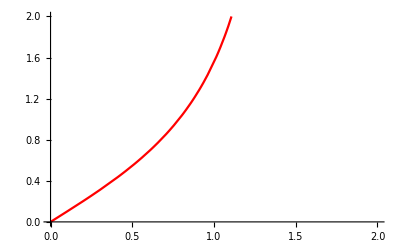

```mathematica
Plot[Tan[x],{x,0,10},PlotRange-> {{0,2},{0,2}},PlotStyle-> Red]
```

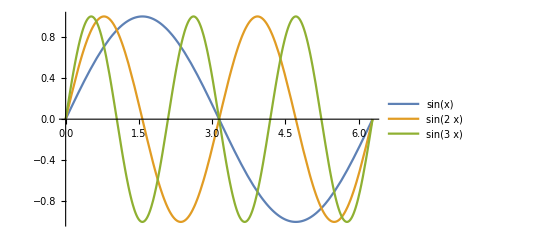

```mathematica
Plot[{Sin[x],Sin[2x],Sin[3x]},{x,0,2Pi},PlotLegends->"Expressions"]
```

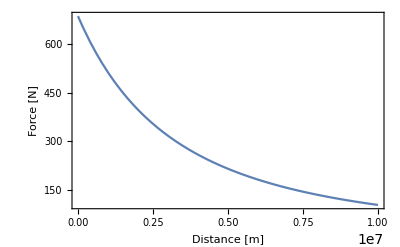

```mathematica
Plot[GravForce[h],{h,0,1*^7},Frame->True,FrameLabel->{"Distance [m]","Force [N]"}]
```

```mathematica
m={5*^24,5*^23}
```

{5000000000000000000000000,500000000000000000000000}

```mathematica
Plot[GravForce[h,m],{h,0,1*^7},Frame->True,FrameLabel->{"Distance [m]","Force [N]"}]
```

-Graphics-

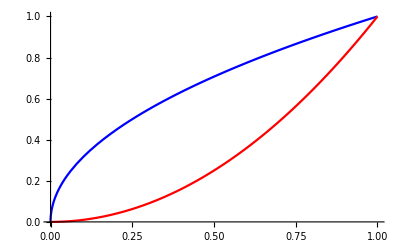

```mathematica
Plot[{√x,x^2},{x,0,1},PlotStyle-> {Blue,Red}]
```

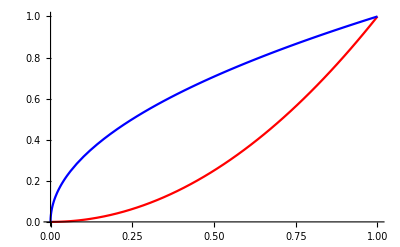

```mathematica
p1=Plot[x^2,{x,0,1},PlotStyle-> Red];
p2=Plot[√x,{x,0,1},PlotStyle-> Blue];
Show[p1,p2]
```

```mathematica
Show[p1,p2]
```

-Graphics-

Lists/Tables/Arrays etc

```mathematica
squareTable = Table[x^2,{x,0,9,2}]
```

{0,4,16,36,64}

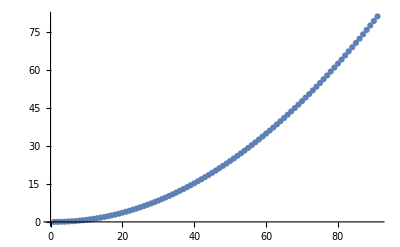

```mathematica
ListPlot[squareTable]
```

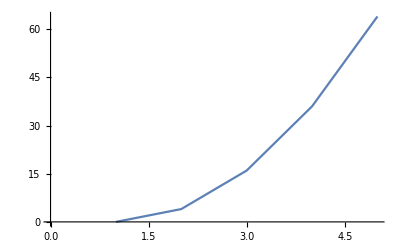

```mathematica
p3=ListLinePlot[squareTable]
```

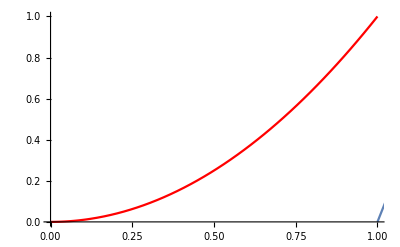

```mathematica
Show[p1,p3]
```

Calculus

```mathematica
f[x_]=x^2
```

x^2

```mathematica
D[f[x],x]
```

2 x

```mathematica
Integrate[f[x],x]
```

x^3/3

```mathematica
∫x^3
```

Integrate::nodiffd: ∫x^3 cannot be interpreted. Integrals are entered in the form ∫fⅆx, ∫_a^b , or ∫_(vars ∈ region) , where ⅆ is entered as EscddEsc.

```mathematica
∫x^2 ⅆx
```

x^3/3

```mathematica
m (d^2 y)/dt^2= -y
```

```mathematica
DSolve[{y''[t]== -y[t],y[0]==0},y[t],t]
```

{{y[t]→C[2] Sin[t]}}